```mathematica
dadosEuler = Import["/home/joao/Documents/1MEFT/2.ba ano/2.ba Ano 1.ba Semestre/FC/2017_2018/Laboratorio/Series/s3c2/s3c2a/Euler.dat", "Table"];
```

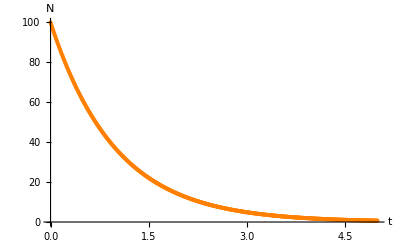

```mathematica
figEuler = ListPlot[dadosEuler, AxesLabel->{"t", "N"}, PlotRange->Full, PlotStyle->Orange]
```

```mathematica
dadosDecaimento = Import["/home/joao/Documents/1MEFT/2.ba ano/2.ba Ano 1.ba Semestre/FC/2017_2018/Laboratorio/Series/s3c2/s3c2a/Analica_Decaimento.dat", "Table"];
```

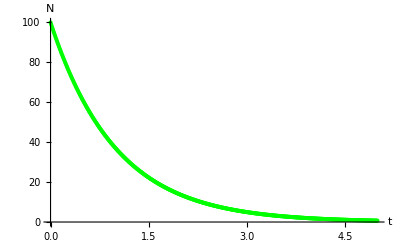

```mathematica
figDecaimento= ListPlot[dadosDecaimento, AxesLabel->{"t", "N"}, PlotRange->Full, PlotStyle->Green]
```

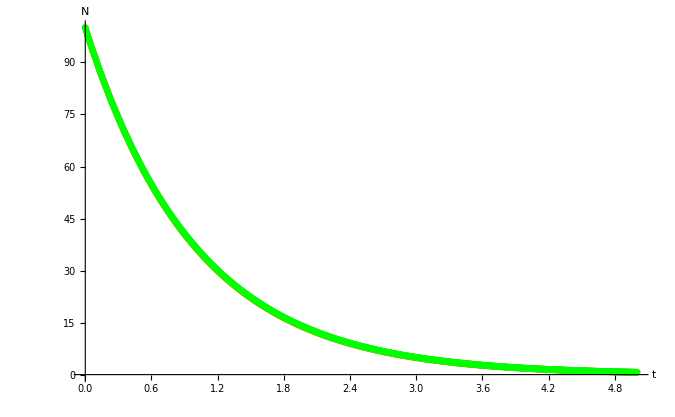

```mathematica
sobrePos = Show[figEuler, figDecaimento]
```

```mathematica
Export["/home/joao/Documents/1MEFT/2.ba ano/2.ba Ano 1.ba Semestre/FC/2017_2018/Laboratorio/Series/s3c2/s3c2a/sobreposição.pdf", sobrePos,"PDF"]
```

/home/joao/Documents/1MEFT/2.ba ano/2.ba Ano 1.ba Semestre/FC/2017_2018/Laboratorio/Series/s3c2/s3c2a/sobreposição.pdf

```mathematica
N0 = 100
```

```mathematica
decay[t_, l_] := N0*Exp[-(l * t)]
```

```mathematica
Manipulate[Plot[decay[t, l], {t, 0, 10}, PlotRange->Full], {l, 0, 4, 0.01} ]
```